```mathematica
(*replace with your download dir*)files=Flatten@With[{dir=NotebookDirectory[]},FileNames["*.eps",dir,3]];
```

```mathematica
Clear@CardData
SetAttributes[CardData,Listable]
StringCases[Last@FileNameSplit@#,card__~~".eps":>(CardData[card]=ImageCrop@Import@#)]&/@files;
```

```mathematica
deck=(Flatten@With[{ranks=CharacterRange["2","9"]~Join~{"10","J","Q","K","A"},suits={"C","S","H","D"}},Outer[StringJoin,ranks,suits]])~Join~{"*R","*B"};
dealHand[n_Integer]/;1≤n≤54:=RandomSample[deck,n]
```

```mathematica
dealHand[5]
```

{9D,KC,*B,QH,8C}

```mathematica
order={"A"}~Join~(ToString/@Range[2,10])~Join~{"J","Q","K","*"}
```

{A,2,3,4,5,6,7,8,9,10,J,Q,K,*}

```mathematica
compare[card1_,card2_]:=Position[order,StringDrop[card1,-1]][[1,1]]-Position[order,StringDrop[card2,-1]][[1,1]]
```

```mathematica
compare["AH","2S"]
```

-1

```mathematica
next[{{X_,Xs___},{Y_,Ys___},{Zs___}}]/;compare[X,Y]<0:={{Xs},{Ys,Zs,X,Y},{}}
next[{{X_,Xs___},{Y_,Ys___},{Zs___}}]/;compare[X,Y]>0:={{Xs,Zs,Y,X},{Ys},{}}
next[{{X_,Xs___},{Y_,Ys___},{Zs___}}]/;compare[X,Y]==0:=Module[{n=Max[Min[3,Length[{Xs}]-1,Length[{Ys}]-1],0]},
{Drop[{Xs},n],Drop[{Ys},n],{Zs}~Join~RandomSample[{X,Y}~Join~Take[{Xs},n]~Join~Take[{Ys},n]]}
]
next[g_]:=g
```

```mathematica
start[]:=Module[{hand=dealHand[27]},
{hand,RandomSample[Complement[deck, hand],27],{}}
]
```

```mathematica
game[]:=Most[FixedPointList[next,start[]]]
```

```mathematica
AbsoluteTiming[g=game[];]
```

{0.001149,Null}

```mathematica
g[[-1]]
```

{{},{4S,8H,6D,QS,JC,5C,6C,5D,6H,KS,10S,2C,AD,3D,10D,QD,10C,7S,8D,7H,4H,9C,3H,4D,*R,3C,2H,8S,7C,AC,10H,JS,AS,5S,KD,KC,QH,KH,9S,4C,5H,8C,JH,QC,9H,6S,9D,JD,*B,2S,AH,2D,3S,7D},{}}

```mathematica
g[[-3]]
```

{{AH,3S},{2D,7D,4S,8H,6D,QS,JC,5C,6C,5D,6H,KS,10S,2C,AD,3D,10D,QD,10C,7S,8D,7H,4H,9C,3H,4D,*R,3C,2H,8S,7C,AC,10H,JS,AS,5S,KD,KC,QH,KH,9S,4C,5H,8C},{JH,QC,9H,6S,9D,JD,*B,2S}}

```mathematica
DisplayGame[g_,Δ_:1]:=
Module[{c},
Print[Dynamic[c]];
Do[
c={CardData/@t[[{1,2}]][[All,1]],(Length/@t)-{1,1,-2}};
Pause[Δ],
{t,Most[g]}]
]
```

```mathematica
DisplayGame[game[]]
```

$Aborted

```mathematica
games=Table[game[],{10000}];//AbsoluteTiming
```

{55.5332,Null}

```mathematica
Length[games]
```

10000

```mathematica
p=Position[Length/@games,Max@@(Length/@games)][[1,1]]
```

6116

```mathematica
Length[games[[p]]]
```

1747

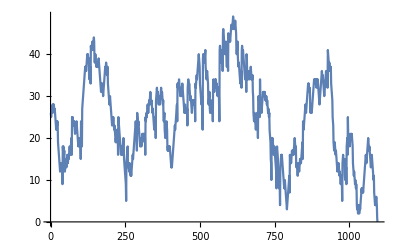

```mathematica
ListPlot[Length/@games[[p]][[All,1]],"Joined"->True]
```

```mathematica
DisplayGame[games[[p]],0.01]
```

```mathematica
q=Position[Length/@games,Min@@(Length/@games)][[1,1]]
```

6460

```mathematica
Length[games[[q]]]
```

12

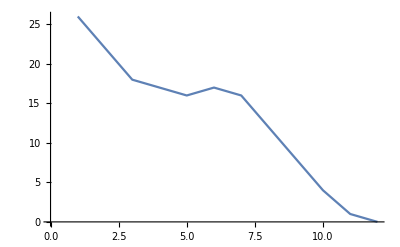

```mathematica
ListPlot[Length/@games[[q]][[All,1]],"Joined"->True]
```

```mathematica
DisplayGame[games[[q]],1]
```

```mathematica
(lengths=Length/@games;)//AbsoluteTiming
```

{0.004908,Null}

```mathematica
Max[lengths]
```

1747

```mathematica
N[Mean[lengths]]
```

257.016

```mathematica
N[StandardDeviation[lengths]]
```

168.747

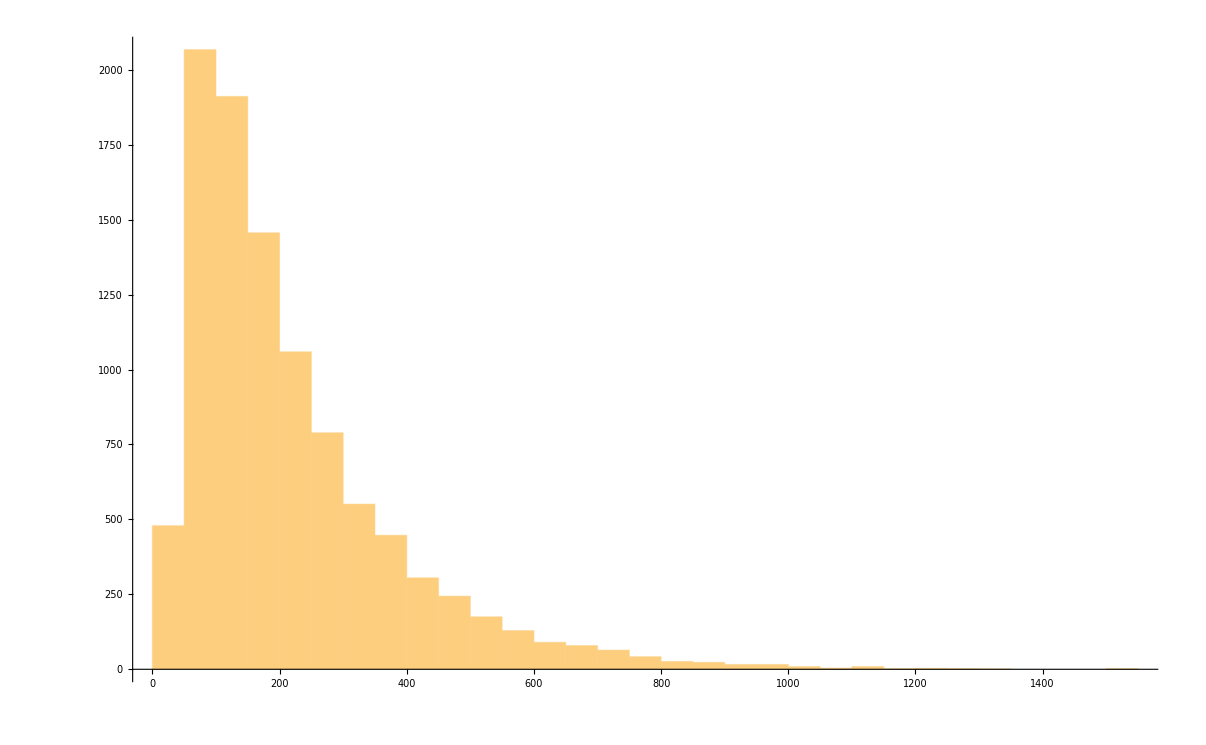

```mathematica
Histogram[lengths,PlotRange->All]
```